```mathematica
VarTablefunc[{prey1_,prey2_}] := (
VarZTable=Table[
nprey = 12;
EX = {-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-16.0,-17.0,-15.8,-13.3,-17.5,-16.2};
VarX = {1.00,0.81,0.49,0.81,0.81,0.81,0.25,1.21,0.64,1.21,1.96,1.00};
Dparam =Table[1,{nprey}];
Dparam[[prey1;;prey2]] = a;
a0 = Total[Dparam];
Ep = N[Dparam/a0];
Varp = N[Table[(Dparam[[i]]*(a0-Dparam[[i]]))/(a0^2*(a0+1)),{i,1,nprey}]];
Covp = N[Table[(-Dparam[[i]]*Dparam[[j]])/(a0^2*(a0+1))Boole[i ≠ j],{i,1,nprey},{j,1,nprey}]];
VarZ = N[Sum[Varp[[i]]*VarX[[i]] + Ep[[i]]^2*VarX[[i]] + EX[[i]]^2*Varp[[i]] + Sum[Covp[[i]][[j]]*EX[[i]]*EX[[j]]Boole[i ≠ j],{j,1,nprey}],{i,1,nprey}]];
propi = a/a0;
{propi,VarZ},
{a,1,1000,1}];
VarXTable = Table[{VarZTable[[i]][[1]],(λ*VarZTable[[i]][[2]])/2},{λ,0,1,0.1},{i,1,Length[VarZTable]}];
Return[{VarZTable,VarXTable}];
)
```

```mathematica
Var7 = VarTablefunc[{7,7}];VarZTable7 = Var7[[1]];VarXTable7 = Var7[[2]];
Var8 = VarTablefunc[{8,8}];VarZTable8 = Var8[[1]];VarXTable8 = Var8[[2]];
Var78 = VarTablefunc[{7,8}];VarZTable78 = Var78[[1]];VarXTable78 = Var78[[2]];
```

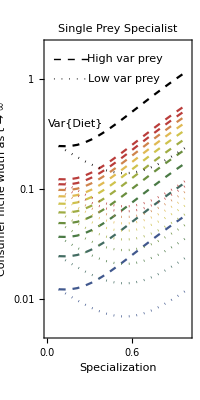
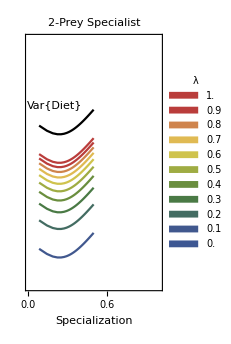

```mathematica
(*Var2 = VarTablefunc[7,8];VarZTable2 = Var2[[1]];VarXTable2 = Var2[[2]];*)
MultipleSpecialistPlot = 
Row[{
Show[{

ListLogPlot[VarZTable8,PlotStyle->Directive[{Black,Dashed}],PlotRange->{{0,1},{0.005,2}},Joined->True,AspectRatio->2,FrameLabel->{"Specialization","Consumer niche width as t → ∞"},Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},Epilog->Style[Text["Var{Diet}",{0.2,Log@0.4}],12],PlotLabel->"Single Prey Specialist"],
Table[
ListLogPlot[VarXTable8[[i+1]],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->Directive[Dashed,ColorData["DarkRainbow",i/10]],Joined->True],{i,1,10,1}],

ListLogPlot[VarZTable7,PlotStyle->Directive[{Black,Dotted}],PlotRange->{{0,1},{0.005,2}},Joined->True,Epilog->Style[Text["Var{Z}",{0.15,Log@0.3}],12]],
Table[
ListLogPlot[VarXTable7[[i+1]],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->Directive[Dotted,ColorData["DarkRainbow",i/10]],Joined->True],{i,1,10,1}],

Graphics[{Thick,Dashed,Line[{{0.05,Log@1.5},{0.3,Log@1.5}}]}],
Graphics[{Thick,Dotted,Line[{{0.05,Log@1},{0.3,Log@1}}]}],

Graphics[Text[Style["High var prey"],{0.55,Log@1.5}]],
Graphics[Text["Low var prey",{0.54,Log@1}]]

},ImageSize->200],

Show[{
ListLogPlot[VarZTable78,Frame->True,PlotStyle->Black,PlotRange->{{0,1},{0.005,2}},Joined->True,AspectRatio->2,FrameLabel->{"Specialization",""},FrameTicks->{{None,None},{Automatic,None}},Epilog->Style[Text["Var{Diet}",{0.2,Log@0.4}],12],PlotLabel->"2-Prey Specialist"],
ListLogPlot[VarXTable78,PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->"DarkRainbow",PlotLegends->SwatchLegend[Table[λ,{λ,0,1,0.1}],LegendLabel->"λ",LegendFunction->(#&),LegendMargins->1,LegendLayout->{"ReversedColumn",1}],Joined->True]
},ImageSize->172]
}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichespecialist.pdf",MultipleSpecialistPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichespecialist.pdf

Variance as a function of the dispersion parameter

```mathematica
VarZGamma = Table[
nprey = 12;
EX = {-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-16.0,-17.0,-15.8,-13.3,-17.5,-16.2};
VarX = {1.00,0.81,0.49,0.81,0.81,0.81,0.25,1.21,0.64,1.21,1.96,1.00};
timebetweenencounters =Table[5,{nprey}];
Dparam = Table[v/timebetweenencounters[[i]],{i,1,12}];
a0 = Total[Dparam];
Ep = N[Dparam/a0];
Varp = N[Table[(Dparam[[i]]*(a0-Dparam[[i]]))/(a0^2*(a0+1)),{i,1,nprey}]];
Covp = N[Table[(-Dparam[[i]]*Dparam[[j]])/(a0^2*(a0+1))Boole[i ≠ j],{i,1,nprey},{j,1,nprey}]];
VarZ = N[Sum[Varp[[i]]*VarX[[i]] + Ep[[i]]^2*VarX[[i]] + EX[[i]]^2*Varp[[i]] + Sum[Covp[[i]][[j]]*EX[[i]]*EX[[j]]Boole[i ≠ j],{j,1,nprey}],{i,1,nprey}]];
VarDiet = (1-Sum[Ep[[i]]^2, {i,1,nprey}])/(nprey*(a0 + 1));
{VarDiet,VarZ},
{v,0.01,1000,0.1}];
VarXGamma = Table[{VarZGamma[[i]][[1]],(λ*VarZGamma[[i]][[2]])/2},{λ,0,1,0.1},{i,1,Length[VarZGamma]}];
```

```mathematica
Total[Ep]
```

1.

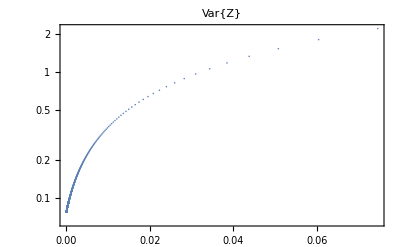

```mathematica
ListLogPlot[VarZGamma,PlotRange->All,Frame->True,PlotLabel->"Var{Z}"]
```

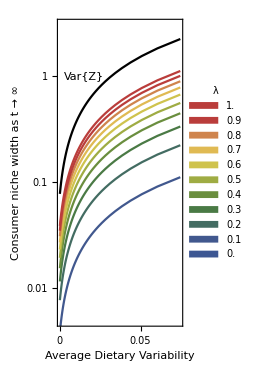

```mathematica
VarSpatialPlot = Show[{
ListLogPlot[VarZGamma,Frame->True,PlotStyle->Black,PlotRange->{All,{0.005,3}},Joined->True,AspectRatio->2,FrameLabel->{"Average Dietary Variability","Consumer niche width as t → ∞"},Epilog->Style[Text["Var{Z}",{0.015,Log@1}],12],FrameTicks->{{All,None},{{0,0.01,0.03,0.05,0.07},None}}],
ListLogPlot[VarXGamma,PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->"DarkRainbow",PlotLegends->SwatchLegend[Table[λ,{λ,0,1,0.1}],LegendLabel->"λ",LegendFunction->(#&),LegendMargins->1,LegendLayout->{"ReversedColumn",1}],Joined->True]
},ImageSize->193]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichegamma.pdf",VarSpatialPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichegamma.pdf

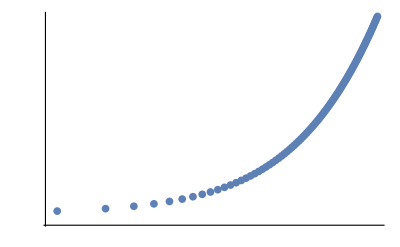

```mathematica
ListLogLogPlot[VarZGamma,Ticks->None]
```

```mathematica
VarXTable3D = Table[{λ,Log[VarZTable[[i]][[1]]],(λ*VarZTable[[i]][[2]])/2},{λ,0,1,0.1},{i,1,Length[VarZTable]}];
```

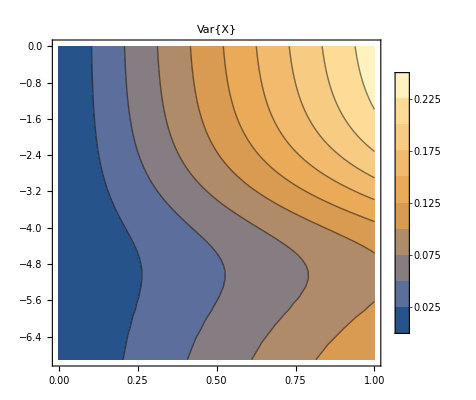

```mathematica
ListContourPlot[Flatten[VarXTable3D,1],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotLegends->True]
```